# Logbook 16014073 Cellular automata II - Modelling Traffic by: Gergely Eory

```mathematica
Unprotect[$ProcessorCount];
$ProcessorCount=4;      (*set this to the maximum number of threads available*)
LaunchKernels[];
SetDirectory[NotebookDirectory[]];
```

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

The first bit of code is not directly related to the workings of the project, yet it is essential to make it more efficient to run. The first three lines tell Mathematica to use all the 4 processing threads available on my CPU, and launches the appropriate number of parallel kernels.  Many of the calculations used during the project are Table functions to generate series of data for different parameters. In most cases, the Table function is embarrassingly parallel, as the results of one value of the iterator variable do not depend on the value of the variable at any other iterations. Instead they are independent, so can be calculated in parallel.
The last line sets the Mathematica’s Directory variable to the location the notebook is stored. When exporting or importing files, Mathematica will automatically look for files in this directory, negating the need for specifying a complete filepath, and ensures smooth operation on any system, as long as the data files are stored in the same directory as the notebook.

#### 2018. Jan. 28.

The Cellular Automaton model is bases on an initial configuration of cells, and an update function that generates new iterations of the cells, based on the current state. Cells in this model are a list of 2 elements.

```mathematica
cell={isCar,speed}
car={1,4}
emptyCell= {0,0}
```

{isCar,speed}

{1,4}

{0,0}

The first element of the list is 1 if a car is occupying the given cell, and 0 otherwise. The second element specifies the speed of the car in the cell. The above example shows a car travelling with v=4, and an empty cell of the road.
The first function generates a initial configuration of the cells, called a “seed”.

```mathematica
generateSeed[freq_,v_,t_]:=Module[{frequency=freq,vmax=v,track=t},(roadd=Table[{0,0},track];
Do[If[RandomReal[]<frequency,roadd[[i]] = {1,0}],{i,1,track}];
Do[If[roadd[[i]] == {1,0}, roadd[[i]] = {1,RandomInteger[{1,vmax}]}],{i,1,track}];
roadd)]
```

It creates a road of length t,then it takes the density of traffic, and fills up each of the cells with cars according to this probability. Then for each car it assigns a random initial speed between 1 and the maximum allowed speed on the road. This function does not guarantee the exact number of cars on the road, but fills up each spot probabilistically. For investigating effects of parameters as a function of traffic density, a well-known controlled parameter is needed.
An updated version of the function was implemented on 2018.Jan.31

```mathematica
generateSeed[frequency_,vmax_,track_]:=(
ncars=Floor[track*frequency];
cars=RandomSample[Range[track],ncars];
road=Table[{0,0},track];
Do[road[[cars[[i]]]]={1,0},{i,1,ncars}];
Do[If[road[[i]] == {1,0}, road[[i,2]] = RandomInteger[{1,vmax}]],{i,1,track}];
Return[road];
)

testSeed=generateSeed[0.2,5,300];
```

This function first calculates the exact number of cars that need to be placed on the road. Then it creates a Random sample, which defines at which positions of the road will there be a car. Then it fills up those positions on the road, and assigns a random starting speed as the previous one.

The next step was the update function, which returns an updated state of the road.
The update function to implement was given in the project specification as follows:

• If the velocity v of the car is lower than vmax , and the distance to the next car ahead is
larger than v + 1, the speed is increased by one.
• If a driver at site i sees the next vehicle at site i+j, with j < v, she reduces speed to j −1.
• The velocity of each vehicle (if greater than zero) is decreased by one with probability p
(‘dawdling’).
• Each vehicle is advanced by v sites.

```mathematica
upd[lanein_List,{vmax_,track_,brakeprob_}]:= (
lane=lanein;
output=Table[{0,0},track];
Do[If[lane[[i,1]]==1 && lane[[i,2]]<vmax,lane[[i,2]]+=1],{i,1,track}];
Do[If[lane[[i,1]]==1 && RandomReal[]<brakeprob&&lane[[i,2]]>0,lane[[i,2]]-=1],{i,1,track}];
Do[If[lane[[i,1]]==1,Do[If[lane[[Mod[(i+j-1),track]+1,1]]==1,(lane[[i,2]]=(j-1);Break[])],{j,1,lane[[i,2]]}]],{i,1,track}];
Do[If[lane[[i,1]]==1,output[[Mod[i+lane[[i,2]]-1,track]+1]]=lane[[i]]],{i,1,track}];
Return[output];
)
```

The model assumes a circular road, meaning the cars which leave the road at one end would appear at the beginning again with the same velocity. This is implemented using modular arithmetic. An thing to note is that modular arithmetic is 0-based, but the numbering of elements of a list in Mathematica starts with 1. For this reason, when referring to element at position i in mod length of the road, we need to  subtract 1 inside the Mod function to make it 0-based, and then add 1 outside to get back the correct numbering. 

Then a function is needed to repeatedly apply the update function to generate traffic data.

```mathematica
generateTraffic[seed_,frequency_,vmax_,brakeprob_,trac_,iterations_]:=(
Module[{track=trac},
If[ListQ[seed],(road=seed;track=Length[seed]),road=generateSeed[frequency,vmax,track]];
traffic=NestList[upd[#,{vmax,track,brakeprob}]&,road,iterations];
Return[traffic];
]
)

testTraffic=generateTraffic[testSeed,0.2,5,0.1,300,300];
```

This function takes a seed, and applies the update function with the specified parameters a chosen number of times, and returns traffic data as a list made up of successive states of the road. Alternatively, if a valid seed is not specified, the function intrinsically generates a seed matching the specified parameters, for cases when different seeds for each simulation are desired.

The next few functions are concerned with plotting and animating the calculated data in various ways. As with most Cellular Automata in Mathematica, the ArrayPlot function is remarkably useful for creating simple visual representations of the data.

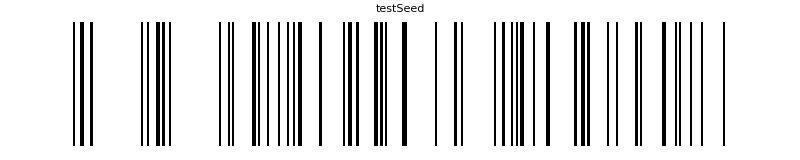

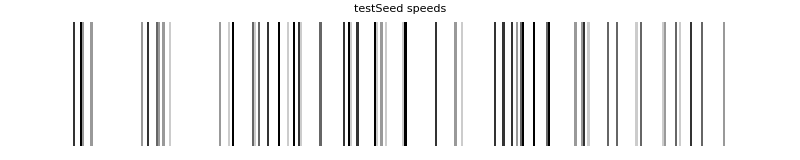

```mathematica
ArrayPlot[{Transpose[testSeed][[1]]},ImageSize->800,PlotLabel->"testSeed"]
ArrayPlot[{Transpose[testSeed][[2]]},ImageSize->800,PlotLabel->"testSeed speeds"]
```

The first plot shows each car with a black dot on the road, while the second one shows the speeds they are moving with, with the greyscale color of each dot.

```mathematica
createArrayPlot[trafficin_List]:=ArrayPlot[Table[trafficin[[i,j,1]],{i,1,Length[trafficin]},{j,1,Length[trafficin[[1]]]}],AspectRatio->Automatic,PixelConstrained->2];

createLaneAnimation[trafficin_List]:=Animate[ArrayPlot[{Table[trafficin[[i,j,1]],{j,1,Length[trafficin[[1]]]}]},ImageSize->Large],{i,1,Length[trafficin],1},AnimationRunning->False];

createArrayPlot[testTraffic]
createLaneAnimation[testTraffic]
```

-Graphics-

Here the first function creates a 2D plot of the traffic data, where each successive line shows the state of the road at each timestep. This already shows some features of traffic, like traffic jams propagating backwards on the road as waves. The visualisations allow an insight into how the simulations model real traffic in an intuitive, easy-to-understand way.
The second function creates an animation, which shows each row of the 2D plot after each other, showing the cars advancing in each timestep.

#### 2018. Jan. 31.

On the 31st of January, the model was extended to be able to handle multiple types of vehicles. This is a scenario where the road is occupied not only by cars, but also trucks, with different allowed maximum speeds.

```mathematica
generateTypeSeed[frequency_,cvmax_,tvmax_,truckratio_,track_]:=(
ncars=Floor[track*frequency];
ntrucks=Floor[ncars*truckratio];
vehicles=RandomSample[Range[track],ncars];
trucks=RandomSample[Range[ncars],ntrucks];
road=Table[{0,0},track];
Do[road[[vehicles[[i]]]]={1,0},{i,1,ncars}];
Do[road[[vehicles[[trucks[[i]]]]]]={2,0},{i,1,ntrucks}];
Do[Which[road[[i]] == {1,0}, road[[i,2]] = RandomInteger[{1,cvmax}],road[[i]] == {2,0}, road[[i,2]] = RandomInteger[{1,tvmax}]],{i,1,track}];
Return[road];
)

testTypeSeed=generateTypeSeed[0.2,5,3,0.2,300];
```

The generateTypeSeed function works very similarly to the updated generateSeed function described in the previous section. In addition to using a RandomSample to place vehicles on the road, it generates another RandomSample to determine which of those vehicles will be trucks, and the rest will be cars. Then in the second step each type of vehicle is assigned a speed, cars ranging from 1 to cvmax, and trucks from 1 to tvmax. The data structure is not altered, but now the number one in a cell specifies a car, while number 2 specifies a truck.
car={1,4}
truck={2,3}
emptyCell={0,0}

A new update function was also created, which takes the different allowed speeds of vehicles into consideration. Similarly, the function which applies the update function to get traffic data was modified to handle the changes.

```mathematica
typeUpd[lanein_List,{cvmax_,tvmax_,track_,brakeprob_}]:=(
lane=lanein;
output=Table[{0,0},track];
Do[Which[(lane[[i,1]]==1 && lane[[i,2]]<cvmax),lane[[i,2]]+=1,(lane[[i,1]]==2 && lane[[i,2]]<tvmax),lane[[i,2]]+=1],{i,1,track}];
Do[If[lane[[i,1]]≠0 && RandomReal[]<brakeprob&&lane[[i,2]]>0,lane[[i,2]]-=1],{i,1,track}];
Do[If[lane[[i,1]]≠0,Do[If[lane[[Mod[(i+j-1),track]+1,1]]≠0,(lane[[i,2]]=(j-1);Break[])],{j,1,lane[[i,2]]}]],{i,1,track}];
Do[If[lane[[i,1]]≠0,output[[Mod[i+lane[[i,2]]-1,track]+1]]=lane[[i]]],{i,1,track}];
Return[output];
)

generateTypeTraffic[seed_,frequency_,cvmax_,tvmax_,brakeprob_,truckratio_,trac_,iterations_]:=(
Module[{track=trac},
If[ListQ[seed],(road=seed;track=Length[seed]),road=generateTypeSeed[frequency,cvmax,tvmax,truckratio,track]];
traffic=NestList[typeUpd[#,{cvmax,tvmax,track,brakeprob}]&,road,iterations];
Return[traffic];
]
)

testTypeTraffic=generateTypeTraffic[testTypeSeed,0.2,5,3,0.1,0.2,300,300];
```

The previously defined visualisation functions still work for the multiple types of vehicles. This time a grey dot shows a car, while a black dot shows a truck.

```mathematica
createArrayPlot[testTypeTraffic]
createLaneAnimation[testTypeTraffic]
```

-Graphics-

Another set of functions were developed to quantitatively investigate the generated data. This allows for separation of the generation and analysis of data. Using these functions, any traffic data in the specified format can be evaluated, without having to know the full set of parameters used during its generation.

```mathematica
numberOfCars[lanein_List]:=Count[Transpose[lanein][[1]],u_/;u≠0];
```

Firstly, a function was implemented to count the number of vehicles in an input traffic data. It simply counts the number of cars in the given lane  or traffic, thus giving a way to extract the traffic density data.

Next, the throughput of the road is measured as the flux of cars (sum of velocities of all cars) passing through the road.

```mathematica
totalThroughput[trafficin_List]:=N[Mean[Table[Total[Transpose[trafficin[[i]]][[2]]],{i,1,Length[trafficin]}]]];
```

This function takes a list representing full traffic data. It calculates the sum of the velocities of all cars at each iteration of the road, then takes the mean of all the results. With simulations running for a few hundred iterations, it gives a good estimate of the throughput of the road resulting from the given initial conditions. The result still depends strongly on the initial state of the road, which will have to be taken into account later. During the traffic investigation, the throughput was the most important quantity considered.

```mathematica
averageSpeed[trafficin_List]:=N[totalThroughput[trafficin]/numberOfCars[trafficin[[1]]]];
```

The average speed of the cars is calculated by dividing the total number of steps advanced by all the cars in each iteration (throughput) by the number of cars.
Both of these functions work for only cars or mixed types of vehicles, as the data structure is the same in both functions.

The set of independent variables in the model are the density of traffic, the maximum speed for each type of car and the probability that cars brake randomly. Now the model is capable of generating traffic data for different values of these variables, which can then be plotted in the desired way. For example, throughput of the road with different densities, ceteris paribus.

```mathematica
throughs=Parallelize[Table[{i,Mean[Table[totalThroughput[generateTraffic["random",i,5,.1,200,100]],{k,1,10}]]},{i,0.05,0.35,0.01}]];
```

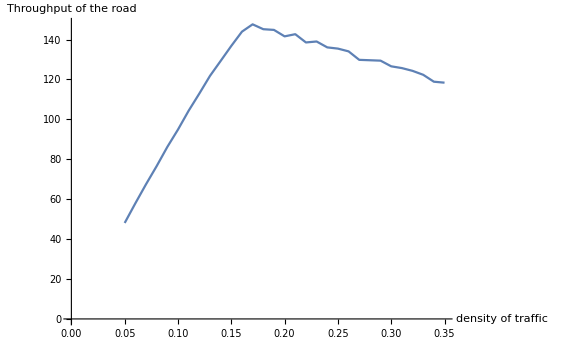

```mathematica
ListPlot[throughs,Joined->True,ImageSize->Large,AxesLabel->{"density of traffic","Throughput of the road"}]
```

The above simulation calculates the throughput of the road 10 times for each density setting from 0.05 to 0.35, and averages them to reduce the uncertainties arising from the possible variations in the initial state of the road, e.g. if the random seed already contained a traffic jam at start. In the report the simulations are ran more times, but the task is computationally demanding, so for purposes of explanation it is reduced to 10 in this case. The number of iterations for each traffic simulation was also reduced sacrificing accuracy for efficiency. For these simulations, the Parallelize function is remarkably useful, as Table functions are embarrassingly parallel.

Investigations of 2 independent variables are also possible.

```mathematica
densitySpeedThroughs=Parallelize[Table[Mean[Table[totalThroughput[generateTraffic["random",i,j,.1,200,100]],{k,1,10}]],{i,0.05,0.30,0.01},{j,3,8}]];
```

```mathematica
densitySpeedThroughs=Transpose[densitySpeedThroughs];
```

-Graphics3D-

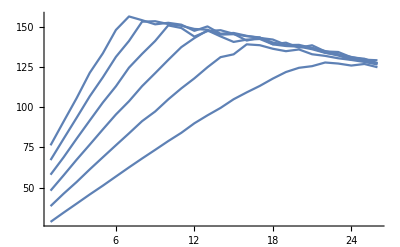

```mathematica
ListPlot3D[densitySpeedThroughs,ImageSize ->Large,AxesLabel->{"density of traffic","max speed","throughput"}]
Show[Table[ListPlot[densitySpeedThroughs[[i]],Joined->True],{i,1,Length[densitySpeedThroughs]}],PlotRange->All]
```

This method can be used to visualize data in a 3D plot as a function of 2 variables, or create separate linear plots on the same graphics panel.

#### 2018.Feb.10-11

In February, multiple attempts were made for extending the model to multiple lanes. This proved challenging, resulting in multiple unfinished functions. The model works by keeping track of he state of the cells of the road, and not by handling individual car objects. Therefore, if in one step a car arrives to an already occupied cell, it overwrites it and all the information about the car previously occupying the cell is lost. In a single lane, this is not a problem, as cars only have to check how far ahead the next car is, and make sure not to run into it. No overtaking is possible so cars do not have to “compete” for the cell. With lane switching, on the other hand, it is possible that cars from multiple lanes try to occupy the same cell, which would result in cars disappearing in thin air. For this reason, the next few unfinished attempts proved unsuccessful.

```mathematica
Do[
If[wannaChange[[l,i,1]]≠0,
Do[
If[road[[l-1,Mod[(i+j-1),track]+1,1]]≠0,
If[wannaChange[[l,i,3]]<(j-1),
For[k=0,k<=cvmax,k++,
If[k==cvmax,CHANGE;Break[]];
If[road[[l-1,Mod[(i-k-1),track]+1,1]]≠0,
If[road[[l-1,Mod[(i-k-1),track]+1,2]]<k,
CHANGE;Break[]
]
]
]
]
],
{j,1,road[[l,i,2]]}
]
],
{i,1,track},{l,2,lanes}
];
```

Do::iterb: Iterator {i,1,track} does not have appropriate bounds.

This attempt from 10th of February aimed to nest If-Else statements to decide whether cars go ahead, or change lanes. the WannaChange function would contain information about which lane the car was aiming to progress in, and the checks for safety would be performed accordingly. After some trying, this approach was abandoned.

```mathematica
Do[If[road[[l,i,1]]≠0,Do[If[road[[l,Mod[(i+j-1),track]+1,1]]≠0,wannaChange[[l,i]]=Append[road[[l,i]],(j-1)]];Break[],{j,1,road[[l,i,2]]}]],{i,1,track},{l,1,lanes}];
Do[If[wannaChange[[l,i,1]]≠0,goAhead[[l,i]]={0,0}],{i,1,track},{l,1,lanes}];
Do[If[wannaChange[[l,i,1]]≠0,Do[If[road[[l-1,Mod[(i+k-1),track]+1,1]]≠0,If[k>road[[l,i,3]],wannaLeft[[l,i]]=Append[wannaChange[[l,i]],k];Break[]],If[k==road[[l,i,2]],wannaLeft[[l,i]]=Append[wannaChange[[l,i]],k];Break[]]],{k,1,road[[l,i,2]]}]],{i,1,track},{l,2,lanes}];
Do[If[wannaChange[[l,i,1]]≠0,Do[If[road[[l+1,Mod[(i+k-1),track]+1,1]]≠0,If[k>road[[l,i,3]],wannaRight[[l,i]]=Append[wannaChange[[l,i]],k];Break[]],If[k==road[[l,i,2]],wannaRight[[l,i]]=Append[wannaChange[[l,i]],k];Break[]]],{k,1,road[[l,i,2]]}]],{i,1,track},{l,1,lanes-1}];
Do[If[wannaChange[[l,i,1]]≠0&&wannaLeft[[l,i,1]]==0&&wannaRight[[l,i,1]]==0,goAhead[[l,i]]==First[Partition[wannaChange[[l,i]],2]]],{i,1,track},{l,1,lanes}];
Do[If[wannaLeft[[l,i,1]]≠0,Do[If[road[[l-1,Mod[(i-k-1),track]+1,1]]≠0,If[road[[l-1,Mod[(i-k-1),track]+1,2]]<k,safeLeft[[l,i]]=wannaLeft[[l,i]]],If[k==cvmax,safeLeft[[l,i]]=wannaLeft[[l,i]]]],{k,0,cvmax}]],{i,1,track},{l,2,lanes}];
Do[If[wannaRight[[l,i,1]]≠0,Do[If[road[[l+1,Mod[(i-k-1),track]+1,1]]≠0,If[road[[l+1,Mod[(i-k-1),track]+1,2]]<k,safeRight[[l,i]]=wannaRight[[l,i]]],If[k==cvmax,safeRight[[l,i]]=wannaRight[[l,i]]]],{k,0,cvmax}]],{i,1,track},{l,1,lanes-1}];
```

Do::iterb: Iterator {i,1,track} does not have appropriate bounds.

The next attempt from 11th of February was aiming to sort the cars into separate lists, depending on where they would progress. Cars would “want to change” if they could progress further in a side lane than in their own. Then they need to check if it is safe to switch lanes, or they would cut in front of another car coming from behind in the other lane. If the change was determined to be unsafe, the cars were removed from the list of cars wanting to switch to that particular lane. In the end, cars would remain in one of 3 lists. One switching to the left lane, one to the right, and the rest would go ahead in their own lane. This bit of code is extremely inefficient with many Do loops and nested If statements, but most importantly, the approach is fundamentally flawed.

#### Violating causality for road safety

The main flaw of previous attempts was the synchronous time approach used in single lane simulations. In the previous sections, it was determined for each car how fat they would progress based on the current state of the road, then they all moved at the same time. That approach does not work for more than 2 lanes, illustrated by a simple example. Suppose there are 3 lanes in a road, A,B and C side by side. There are 2 cars in the side lanes A and C, that would both want to switch to lane B. They could both check if such a switch would be safe, and get a positive result, and in the end they would both switch, possibly leading to a collision (one of the cars being overwritten). To avoid the collision, the cars would have to possess information about the intentions of the cars 2 lanes away in addition to knowing their position, and know when they would also want to change before they actually move. In theory it is possible, but the principles of the CA model assume that the cells are updated solely based on the current state of the cells. Such problems do not arise in real life, where drivers all perceive time linearly and simultaneously, and can use indicator lights to signal their intentions.
The solution implemented circumvents this problem, by changing to a “rolling update” scheme. In each iteration of the update function, cars check where they want to go one by one, then immediately advance to the best possible cell. In this scheme, each car only needs to be concerned with the current state of the road to make a decision. On the other hand, the scheme violates causality, as different cars on the road experience time in different instances, and cars can appear to have overtaken others before they even check where to go. Still in terms of the simulation it is very efficient, as cars do not need to check if cars are coming from behind in the other lane or not. Instead, the other car would take care of that evaluation when it comes to their turn to move.

#### 2018. Feb. 28 - Multilane solution

```mathematica
generateMultiSeed[frequency_,cvmax_,tvmax_,truckratio_,track_,lanes_]:=(
Table[generateTypeSeed[frequency,cvmax,tvmax,truckratio,track],{i,1,lanes}]
)

testMultiSeed=generateMultiSeed[0.2,5,3,0.0,300,4];
```

The seed generation for a multilane simulation is a simple table of n single lanes where n is the number of lanes.
On 17th of March, a new version of the multilane seed generator was created, which only places trucks in the two rightmost lanes.

```mathematica
generateTypeMultiSeed[frequency_,cvmax_,tvmax_,truckratio_,track_,lanes_]:=(
Flatten[{{generateTypeSeed[frequency,cvmax,tvmax,truckratio,track]},{generateTypeSeed[frequency,cvmax,tvmax,truckratio,track]},Table[generateSeed[frequency,cvmax,track],{i,1,lanes-2}]},1]
)
```

This function generates 2 lanes with trucks, and l-2 lanes with cars only with l representing the total number of lanes. Then it flattens the first level of the lists such that the road is in the same data format as seen before. The update function was not modified.

```mathematica
howManyAhead[road_List,l_,i_,{track_,lanes_}]:=(
output={"null","null","null"};
Do[
If[road[[l,Mod[(i+j-1),track]+1,1]]≠0 &&output[[1]]=="null",output[[1]]=j-1];If[l≠1,If[road[[l-1,Mod[(i+j-1),track]+1,1]]≠0 &&output[[2]]=="null",output[[2]]=j-1]];If[l≠lanes,If[road[[l+1,Mod[(i+j-1),track]+1,1]]≠0 &&output[[3]]=="null",output[[3]]=j-1]],
{j,1,road[[l,i,2]]}];
Do[If[output[[k]]=="null",output[[k]]=road[[l,i,2]]],{k,1,3}];
If[l==1,output[[2]]=0];
If[l==lanes,output[[3]]=0];
Return[output];
)
```

The multilane update function uses an auxiliary function, howManyAhead, which calculates how many steps a car in a specified position can advance in its own lane and the 2 lanes adjacent to it. The function also takes into account that if the car is in a lane at the side of the road, it can only advance ahead or switch to one side lane. In this sense, the road is NOT assumed to be circular. (For the geometrically inclined reader, the road mimics a Möbius strip, not a torus.)

```mathematica
multiUpd[roadin_List,{cvmax_,tvmax_,track_,brakeprob_,lanes_}]:=(
road=roadin;
output=Table[Table[{0,0},track],lanes];
distances={0,0,0};
Do[Which[(road[[l,i,1]]==1 && road[[l,i,2]]<cvmax),road[[l,i,2]]+=1,(road[[l,i,1]]==2 && road[[l,i,2]]<tvmax),road[[l,i,2]]+=1],{i,1,track},{l,1,lanes}];
Do[If[road[[l,i,1]]≠0 && RandomReal[]<brakeprob&&road[[l,i,2]]>0,road[[l,i,2]]-=1],{i,1,track},{l,1,lanes}];
Do[If[road[[l,i,1]]≠0&&Length[road[[l,i]]]==2,
distances=howManyAhead[road,l,i,{track,lanes}];
If[distances[[1]]<distances[[2]],
If[distances[[2]]<distances[[3]],  (*Contains preference to keep to the -1 side*)
road[[l,i,2]]=distances[[3]];road[[l+1,Mod[(i+distances[[3]]-1),track]+1]]=AppendTo[road[[l,i]],"moved"];road[[l,i]]={0,0},
road[[l,i,2]]=distances[[2]];road[[l-1,Mod[(i+distances[[2]]-1),track]+1]]=AppendTo[road[[l,i]],"moved"];road[[l,i]]={0,0}],
If[distances[[1]]<distances[[3]],
road[[l,i,2]]=distances[[3]];road[[l+1,Mod[(i+distances[[3]]-1),track]+1]]=AppendTo[road[[l,i]],"moved"];road[[l,i]]={0,0},
road[[l,i,2]]=distances[[1]];road[[l,Mod[(i+distances[[1]]-1),track]+1]]=AppendTo[road[[l,i]],"moved"];road[[l,i]]={0,0}]]],
{i,1,track},{l,1,lanes}];
Do[If[Length[road[[l,i]]]==3,road[[l,i]]=First[Partition[road[[l,i]],2]]],{i,1,track},{l,1,lanes}];
Return[road];
)
```

The first two parts of the multilane  update function are the same as before. Each car’s speed is incremented, and some are randomly decremented according to the brake probability.
As mentioned before, the next part of the function works sequentially on each cell of the road. The function sweeps through the road lane by lane, from position one to the end of the lane. If it finds a car, it checks if it has already moved in the current iteration of the update function. If the car has not moved yet, Through a series of If statements it determines in which lane the car can advance the furthest, and moves it to that lane. If two values are equal, preference is given for going straight ahead, then to move to the lane to the left. This mimics highway regulations which state that cars should aim to keep left on the motorway when possible. When a car moves, a “moved” tag also gets appended to it. For each car the function checks if the car has already moved, so if a car ends up in a higher number lane, it will not move again as the function sees it on the road again. At the very end, the “moved” tags get dropped from each car, so the list will have the same dimensions and information as in the beginning.

```mathematica
generateMultiTraffic[seed_,frequency_,cvmax_,tvmax_,brakeprob_,truckratio_,trac_,lane_,iterations_]:=(
Module[{track=trac,lanes=lane},
If[ListQ[seed],(road=seed;lanes=Length[seed];track=Length[seed[[1]]]),road=generateMultiSeed[frequency,cvmax,tvmax,truckratio,track,lanes]];
traffic=NestList[multiUpd[#,{cvmax,tvmax,track,brakeprob,lanes}]&,road,iterations];
Return[traffic];
]
)

testMultiTraffic=generateMultiTraffic[testMultiSeed,0.15,5,3,0.1,0,300,5,200];
```

As before, there is a function to generate multiple lane traffic data, that applies the update function to the road a specified number of times. 
The functions to calculate throughput and average speed were also modified to handle multiple lane traffic data.

```mathematica
totalMultiThroughput[trafficin_List]:=N[Mean[Table[Total[Flatten[Last[Transpose[trafficin[[i]],{2,3,1}]]]],{i,1,Length[trafficin]}]]];
```

This function uses Mathematica’s built in list-manipulation functions to extract the speed data and calculate the total throughput of the multiple lane road in an efficient manner.

```mathematica
numberOfMultiCars[trafficin_List]:=Sum[numberOfCars[trafficin[[1,j]]],{j,1,Length[trafficin[[1]]]}];

averageMultiSpeed[trafficin_List]:=N[totalMultiThroughput[trafficin]/numberOfMultiCars[trafficin]];
```

These two functions calculate the number of cars in a multi-lane road, and the average speed of the cars in an input multilane traffic data.

```mathematica
createMultiAnimation[trafficin_List]:=Animate[ArrayPlot[Table[trafficin[[i,j,k,1]],{j,1,Length[trafficin[[1]]]},{k,1,Length[trafficin[[1,1]]]}],ImageSize->Large],{i,1,Length[trafficin],1},AnimationRunning->False];
createMultiAnimation[testMultiTraffic]
```

This function creates an animation of the road with multiple lanes shown parallel to each other.

Creating an ArrayPlot for multiple lanes proved more challenging though, as ArrayPlots cannot be made 3 dimensional. The following function shows distinct plots, each corresponding to a different lane of the road.

```mathematica
createMultiPlot[trafficin_List]:=Table[createArrayPlot[Transpose[trafficin][[i]]],{i,1,Length[trafficin[[1]]]}]

createMultiPlot[testMultiTraffic]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### 2018. Mar. 17 - Simulations and plotting

On March 17, simulation results were generated and plotted for the for the report first draft.

```mathematica
through=Parallelize[Table[{i,Mean[Table[totalThroughput[generateTraffic["random",i,5,.1,200,100]],{k,1,10}]]},{i,0.01,0.35,0.01}]];
speed=Parallelize[Table[{i,Mean[Table[averageSpeed[generateTraffic["random",i,5,.1,200,100]],{k,1,10}]]},{i,0.01,0.35,0.01}]];
```

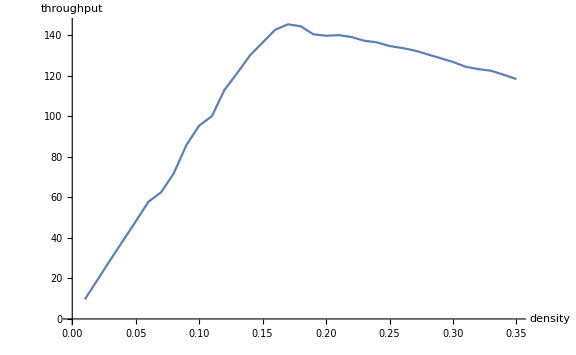
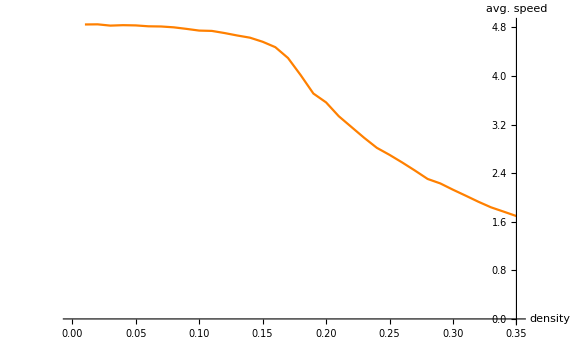

```mathematica
lp1=ListPlot[through,Joined->True,ImageSize->Large,ImagePadding->50,AxesLabel->{"density","throughput"}];
lp2=ListPlot[speed,Joined->True,AxesOrigin->{.35,0},PlotStyle->Orange,ImageSize->Large,ImagePadding->50,AxesLabel->{"density","avg. speed"}];
Overlay[{lp1,lp2}]
```

The Overlay function was used to plot separate aspects of the data on the same graph, with separate Y axes.

#### 2018. Mar. 21 - 23

The traffic simulations were generated and analysed in the days 21-23 of March. Single lane and single variable simulations were run with high number of iterations on my laptop, on an Intel i7-5500U CPU with four parallel threads. simpler simulations took only a few minutes to run, and could be plotted and evaluated almost instantly. 
Simulations with multiple variables and multiple lanes were run on my flatmate’s PC, on an Intel i7-6700K, with 8 parallel threads. The higher clockspeed and double the core count made the simulations run approximately 4 times faster. Still, simulations for section Three and Four took between 30 minutes and 4 hours to run.
The report was written on these 3 days as well, including plotting and evaluating the results gathered.